# Random PoS reward function

## Variables

```mathematica
sequences = 5
n = 210
rewards = List[50*n,25*n,12.5*n,6.25*n,3.125*n]
r =0.03
```

## Constant reward function

```mathematica
constreward[n_,R_,T_]=Table[R/T,n]
```

## Geometric reward function

```mathematica
geometricreward[n_, R_, T_] = Table[(1 + R)^(i/T) - (1 + R)^((i-1)/T),{i,n}]
```

## Random reward function

```mathematica
randomreward[n_, R_, T_] = RandomVariate[UniformDistribution[]+0.5,n]*R/T
```

```mathematica
randomdistribution[n_, R_, T_] = RandomVariate[BetaDistribution[2,5]+0.5,n]*R/T
```

## Interest rate function

```mathematica
interestreward[n_, r_, T_] = (1+r/n)^(n*T)
```

## Comparison

```mathematica
dataconst= Flatten[Table[constreward[runs, rewards[[i]], n],{i,1,sequences}]]
datageometric = Flatten[Table[geometricreward[runs, rewards[[i]], n],{i,1,sequences}]]
datarandom = Flatten[Table[randomreward[runs, rewards[[i]], n],{i,1,sequences}]]
datarandomdist = Flatten[Table[randomdistribution[runs, rewards[[i]], n],{i,1,sequences}]]
plotdata= List[dataconst,datageometric, datarandom, datarandomdist]
```

```mathematica
ListPlot[dataconst,PlotRange -> {0, 1.1* Max[dataconst]}, DataRange->{0,sequences*n}, PlotLabel->"Constant reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Blue}]
ListPlot[datageometric,PlotRange -> {0, 1.1* Max[datageometric]}, DataRange->{0,sequences*n}, PlotLabel->"Geometric reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Red}]
ListPlot[datarandom,PlotRange -> {0, 1.1* Max[datarandom]}, DataRange->{0,sequences*n}, PlotLabel->"Uniform random reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Green}]
ListPlot[datarandomdist,PlotRange -> {0, 1.1* Max[datarandomdist]}, DataRange->{0,sequences*n}, PlotLabel->"Beta distribution-based random reward", AxesLabel->{"Block height", "Reward"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, Filling->Bottom, PlotStyle-> {Purple}]
```

## Fairness

Fairness is defined as the proportional reward depending on the starting stake.

## Equitability (Variance)

```mathematica
reward = 50
stake = 1
time = 1000
```

50

1

1000

```mathematica
varianceconst[R_,T_]=Table[R^2/((i+R) (1+R)),{i,1,time}]
variancegeo[R_,T_]=Table[1-((2 (1+R)^(1/i)-1)^i)/(1+R)^2,{i,1,time}]
varianceuniform[R_, T_, rand_] = Table[(rand[[i]]*R)^2/((i+(rand[[i]]*R)) (1+(rand[[i]]*R))),{i,1,time}]
variancebeta[R_, T_, rand_] = Table[(rand[[i]] * R)^2/((i+(rand[[i]]*R)) (1+(rand[[i]]*R))),{i,1,time}]
```

{R^2/(1+R)^2,R^2/((1+R) (2+R)),R^2/((1+R) (3+R)),R^2/((1+R) (4+R)),R^2/((1+R) (5+R)),R^2/((1+R) (6+R)),R^2/((1+R) (7+R)),R^2/((1+R) (8+R)),R^2/((1+R) (9+R)),R^2/((1+R) (10+R)),980,R^2/((1+R) (991+R)),R^2/((1+R) (992+R)),R^2/((1+R) (993+R)),R^2/((1+R) (994+R)),R^2/((1+R) (995+R)),R^2/((1+R) (996+R)),R^2/((1+R) (997+R)),R^2/((1+R) (998+R)),R^2/((1+R) (999+R)),R^2/((1+R) (1000+R))}
 |  |  |  |

{1-(-1+2 (1+R))/(1+R)^2,1-(-1+2 √(1+R))^2/(1+R)^2,996,1-((-1+2 (1+R)^(1/999))^999)/(1+R)^2,1-((-1+2 (1+R)^(1/1000))^1000)/(1+R)^2}
 |  |  |  |

Part::partd: Part specification rand⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{(R^2 rand⟦1⟧^2)/(1+R rand⟦1⟧)^2,(R^2 rand⟦2⟧^2)/((1+R rand⟦2⟧) (2+R rand⟦2⟧)),(R^2 rand⟦3⟧^2)/((1+R rand⟦3⟧) (3+R rand⟦3⟧)),994,(R^2 rand⟦998⟧^2)/((1+R rand⟦998⟧) (998+R rand⟦998⟧)),(R^2 rand⟦999⟧^2)/((1+R rand⟦999⟧) (999+R rand⟦999⟧)),(R^2 rand⟦1000⟧^2)/((1+R rand⟦1000⟧) (1000+R rand⟦1000⟧))}
 |  |  |  |

Part::partd: Part specification rand⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{(R^2 rand⟦1⟧^2)/(1+R rand⟦1⟧)^2,(R^2 rand⟦2⟧^2)/((1+R rand⟦2⟧) (2+R rand⟦2⟧)),(R^2 rand⟦3⟧^2)/((1+R rand⟦3⟧) (3+R rand⟦3⟧)),994,(R^2 rand⟦998⟧^2)/((1+R rand⟦998⟧) (998+R rand⟦998⟧)),(R^2 rand⟦999⟧^2)/((1+R rand⟦999⟧) (999+R rand⟦999⟧)),(R^2 rand⟦1000⟧^2)/((1+R rand⟦1000⟧) (1000+R rand⟦1000⟧))}
 |  |  |  |

```mathematica
datavarconst = varianceconst[reward, time]
datavargeo = variancegeo[reward, time]
datavaruni = varianceuniform[reward,time, RandomVariate[UniformDistribution[{0.5,1.5}], time]]
datavarbeta = variancebeta[reward,time, RandomVariate[BetaDistribution[2,5], time]+0.5]
```

{2500/2601,625/663,2500/2703,1250/1377,500/561,625/714,2500/2907,1250/1479,2500/3009,125/153,2500/3111,1250/1581,2500/3213,625/816,500/663,1250/1683,2500/3417,625/867,2500/3519,250/357,2500/3621,625/918,2500/3723,1250/1887,100/153,625/969,2500/3927,1250/1989,2500/4029,125/204,2500/4131,1250/2091,2500/4233,625/1071,500/867,1250/2193,2500/4437,625/1122,2500/4539,250/459,2500/4641,625/1173,2500/4743,1250/2397,500/969,625/1224,2500/4947,1250/2499,2500/5049,25/51,2500/5151,1250/2601,2500/5253,625/1326,500/1071,1250/2703,2500/5457,625/1377,2500/5559,250/561,2500/5661,625/1428,2500/5763,1250/2907,500/1173,625/1479,2500/5967,1250/3009,2500/6069,125/306,2500/6171,1250/3111,2500/6273,625/1581,20/51,1250/3213,2500/6477,625/1632,2500/6579,250/663,2500/6681,625/1683,2500/6783,1250/3417,500/1377,625/1734,2500/6987,1250/3519,2500/7089,125/357,2500/7191,1250/3621,2500/7293,625/1836,500/1479,1250/3723,2500/7497,625/1887,2500/7599,50/153,2500/7701,625/1938,2500/7803,1250/3927,500/1581,625/1989,2500/8007,1250/4029,2500/8109,125/408,2500/8211,1250/4131,2500/8313,625/2091,500/1683,1250/4233,2500/8517,625/2142,2500/8619,250/867,2500/8721,625/2193,2500/8823,1250/4437,100/357,625/2244,2500/9027,1250/4539,2500/9129,125/459,2500/9231,1250/4641,2500/9333,625/2346,500/1887,1250/4743,2500/9537,625/2397,2500/9639,250/969,2500/9741,625/2448,2500/9843,1250/4947,500/1989,625/2499,2500/10047,1250/5049,2500/10149,25/102,2500/10251,1250/5151,2500/10353,625/2601,500/2091,1250/5253,2500/10557,625/2652,2500/10659,250/1071,2500/10761,625/2703,2500/10863,1250/5457,500/2193,625/2754,2500/11067,1250/5559,2500/11169,125/561,2500/11271,1250/5661,2500/11373,625/2856,100/459,1250/5763,2500/11577,625/2907,2500/11679,250/1173,2500/11781,625/2958,2500/11883,1250/5967,500/2397,625/3009,2500/12087,1250/6069,2500/12189,125/612,2500/12291,1250/6171,2500/12393,625/3111,500/2499,1250/6273,2500/12597,625/3162,2500/12699,10/51,2500/12801,625/3213,2500/12903,1250/6477,500/2601,625/3264,2500/13107,1250/6579,2500/13209,125/663,2500/13311,1250/6681,2500/13413,625/3366,500/2703,1250/6783,2500/13617,625/3417,2500/13719,250/1377,2500/13821,625/3468,2500/13923,1250/6987,100/561,625/3519,2500/14127,1250/7089,2500/14229,125/714,2500/14331,1250/7191,2500/14433,625/3621,500/2907,1250/7293,2500/14637,625/3672,2500/14739,250/1479,2500/14841,625/3723,2500/14943,1250/7497,500/3009,625/3774,2500/15147,1250/7599,2500/15249,25/153,2500/15351,1250/7701,2500/15453,625/3876,500/3111,1250/7803,2500/15657,625/3927,2500/15759,250/1581,2500/15861,625/3978,2500/15963,1250/8007,500/3213,625/4029,2500/16167,1250/8109,2500/16269,125/816,2500/16371,1250/8211,2500/16473,625/4131,100/663,1250/8313,2500/16677,625/4182,2500/16779,250/1683,2500/16881,625/4233,2500/16983,1250/8517,500/3417,625/4284,2500/17187,1250/8619,2500/17289,125/867,2500/17391,1250/8721,2500/17493,625/4386,500/3519,1250/8823,2500/17697,625/4437,2500/17799,50/357,2500/17901,625/4488,2500/18003,1250/9027,500/3621,625/4539,2500/18207,1250/9129,2500/18309,125/918,2500/18411,1250/9231,2500/18513,625/4641,500/3723,1250/9333,2500/18717,625/4692,2500/18819,250/1887,2500/18921,625/4743,2500/19023,1250/9537,20/153,625/4794,2500/19227,1250/9639,2500/19329,125/969,2500/19431,1250/9741,2500/19533,625/4896,500/3927,1250/9843,2500/19737,625/4947,2500/19839,250/1989,2500/19941,625/4998,2500/20043,1250/10047,500/4029,625/5049,2500/20247,1250/10149,2500/20349,25/204,2500/20451,1250/10251,2500/20553,625/5151,500/4131,1250/10353,2500/20757,625/5202,2500/20859,250/2091,2500/20961,625/5253,2500/21063,1250/10557,500/4233,625/5304,2500/21267,1250/10659,2500/21369,125/1071,2500/21471,1250/10761,2500/21573,625/5406,100/867,1250/10863,2500/21777,625/5457,2500/21879,250/2193,2500/21981,625/5508,2500/22083,1250/11067,500/4437,625/5559,2500/22287,1250/11169,2500/22389,125/1122,2500/22491,1250/11271,2500/22593,625/5661,500/4539,1250/11373,2500/22797,625/5712,2500/22899,50/459,2500/23001,625/5763,2500/23103,1250/11577,500/4641,625/5814,2500/23307,1250/11679,2500/23409,125/1173,2500/23511,1250/11781,2500/23613,625/5916,500/4743,1250/11883,2500/23817,625/5967,2500/23919,250/2397,2500/24021,625/6018,2500/24123,1250/12087,100/969,625/6069,2500/24327,1250/12189,2500/24429,125/1224,2500/24531,1250/12291,2500/24633,625/6171,500/4947,1250/12393,2500/24837,625/6222,2500/24939,250/2499,2500/25041,625/6273,2500/25143,1250/12597,500/5049,625/6324,2500/25347,1250/12699,2500/25449,5/51,2500/25551,1250/12801,2500/25653,625/6426,500/5151,1250/12903,2500/25857,625/6477,2500/25959,250/2601,2500/26061,625/6528,2500/26163,1250/13107,500/5253,625/6579,2500/26367,1250/13209,2500/26469,125/1326,2500/26571,1250/13311,2500/26673,625/6681,100/1071,1250/13413,2500/26877,625/6732,2500/26979,250/2703,2500/27081,625/6783,2500/27183,1250/13617,500/5457,625/6834,2500/27387,1250/13719,2500/27489,125/1377,2500/27591,1250/13821,2500/27693,625/6936,500/5559,1250/13923,2500/27897,625/6987,2500/27999,50/561,2500/28101,625/7038,2500/28203,1250/14127,500/5661,625/7089,2500/28407,1250/14229,2500/28509,125/1428,2500/28611,1250/14331,2500/28713,625/7191,500/5763,1250/14433,2500/28917,625/7242,2500/29019,250/2907,2500/29121,625/7293,2500/29223,1250/14637,100/1173,625/7344,2500/29427,1250/14739,2500/29529,125/1479,2500/29631,1250/14841,2500/29733,625/7446,500/5967,1250/14943,2500/29937,625/7497,2500/30039,250/3009,2500/30141,625/7548,2500/30243,1250/15147,500/6069,625/7599,2500/30447,1250/15249,2500/30549,25/306,2500/30651,1250/15351,2500/30753,625/7701,500/6171,1250/15453,2500/30957,625/7752,2500/31059,250/3111,2500/31161,625/7803,2500/31263,1250/15657,500/6273,625/7854,2500/31467,1250/15759,2500/31569,125/1581,2500/31671,1250/15861,2500/31773,625/7956,4/51,1250/15963,2500/31977,625/8007,2500/32079,250/3213,2500/32181,625/8058,2500/32283,1250/16167,500/6477,625/8109,2500/32487,1250/16269,2500/32589,125/1632,2500/32691,1250/16371,2500/32793,625/8211,500/6579,1250/16473,2500/32997,625/8262,2500/33099,50/663,2500/33201,625/8313,2500/33303,1250/16677,500/6681,625/8364,2500/33507,1250/16779,2500/33609,125/1683,2500/33711,1250/16881,2500/33813,625/8466,500/6783,1250/16983,2500/34017,625/8517,2500/34119,250/3417,2500/34221,625/8568,2500/34323,1250/17187,100/1377,625/8619,2500/34527,1250/17289,2500/34629,125/1734,2500/34731,1250/17391,2500/34833,625/8721,500/6987,1250/17493,2500/35037,625/8772,2500/35139,250/3519,2500/35241,625/8823,2500/35343,1250/17697,500/7089,625/8874,2500/35547,1250/17799,2500/35649,25/357,2500/35751,1250/17901,2500/35853,625/8976,500/7191,1250/18003,2500/36057,625/9027,2500/36159,250/3621,2500/36261,625/9078,2500/36363,1250/18207,500/7293,625/9129,2500/36567,1250/18309,2500/36669,125/1836,2500/36771,1250/18411,2500/36873,625/9231,100/1479,1250/18513,2500/37077,625/9282,2500/37179,250/3723,2500/37281,625/9333,2500/37383,1250/18717,500/7497,625/9384,2500/37587,1250/18819,2500/37689,125/1887,2500/37791,1250/18921,2500/37893,625/9486,500/7599,1250/19023,2500/38097,625/9537,2500/38199,10/153,2500/38301,625/9588,2500/38403,1250/19227,500/7701,625/9639,2500/38607,1250/19329,2500/38709,125/1938,2500/38811,1250/19431,2500/38913,625/9741,500/7803,1250/19533,2500/39117,625/9792,2500/39219,250/3927,2500/39321,625/9843,2500/39423,1250/19737,100/1581,625/9894,2500/39627,1250/19839,2500/39729,125/1989,2500/39831,1250/19941,2500/39933,625/9996,500/8007,1250/20043,2500/40137,625/10047,2500/40239,250/4029,2500/40341,625/10098,2500/40443,1250/20247,500/8109,625/10149,2500/40647,1250/20349,2500/40749,25/408,2500/40851,1250/20451,2500/40953,625/10251,500/8211,1250/20553,2500/41157,625/10302,2500/41259,250/4131,2500/41361,625/10353,2500/41463,1250/20757,500/8313,625/10404,2500/41667,1250/20859,2500/41769,125/2091,2500/41871,1250/20961,2500/41973,625/10506,100/1683,1250/21063,2500/42177,625/10557,2500/42279,250/4233,2500/42381,625/10608,2500/42483,1250/21267,500/8517,625/10659,2500/42687,1250/21369,2500/42789,125/2142,2500/42891,1250/21471,2500/42993,625/10761,500/8619,1250/21573,2500/43197,625/10812,2500/43299,50/867,2500/43401,625/10863,2500/43503,1250/21777,500/8721,625/10914,2500/43707,1250/21879,2500/43809,125/2193,2500/43911,1250/21981,2500/44013,625/11016,500/8823,1250/22083,2500/44217,625/11067,2500/44319,250/4437,2500/44421,625/11118,2500/44523,1250/22287,20/357,625/11169,2500/44727,1250/22389,2500/44829,125/2244,2500/44931,1250/22491,2500/45033,625/11271,500/9027,1250/22593,2500/45237,625/11322,2500/45339,250/4539,2500/45441,625/11373,2500/45543,1250/22797,500/9129,625/11424,2500/45747,1250/22899,2500/45849,25/459,2500/45951,1250/23001,2500/46053,625/11526,500/9231,1250/23103,2500/46257,625/11577,2500/46359,250/4641,2500/46461,625/11628,2500/46563,1250/23307,500/9333,625/11679,2500/46767,1250/23409,2500/46869,125/2346,2500/46971,1250/23511,2500/47073,625/11781,100/1887,1250/23613,2500/47277,625/11832,2500/47379,250/4743,2500/47481,625/11883,2500/47583,1250/23817,500/9537,625/11934,2500/47787,1250/23919,2500/47889,125/2397,2500/47991,1250/24021,2500/48093,625/12036,500/9639,1250/24123,2500/48297,625/12087,2500/48399,50/969,2500/48501,625/12138,2500/48603,1250/24327,500/9741,625/12189,2500/48807,1250/24429,2500/48909,125/2448,2500/49011,1250/24531,2500/49113,625/12291,500/9843,1250/24633,2500/49317,625/12342,2500/49419,250/4947,2500/49521,625/12393,2500/49623,1250/24837,100/1989,625/12444,2500/49827,1250/24939,2500/49929,125/2499,2500/50031,1250/25041,2500/50133,625/12546,500/10047,1250/25143,2500/50337,625/12597,2500/50439,250/5049,2500/50541,625/12648,2500/50643,1250/25347,500/10149,625/12699,2500/50847,1250/25449,2500/50949,5/102,2500/51051,1250/25551,2500/51153,625/12801,500/10251,1250/25653,2500/51357,625/12852,2500/51459,250/5151,2500/51561,625/12903,2500/51663,1250/25857,500/10353,625/12954,2500/51867,1250/25959,2500/51969,125/2601,2500/52071,1250/26061,2500/52173,625/13056,100/2091,1250/26163,2500/52377,625/13107,2500/52479,250/5253,2500/52581,625/13158,2500/52683,1250/26367,500/10557,625/13209,2500/52887,1250/26469,2500/52989,125/2652,2500/53091,1250/26571,2500/53193,625/13311,500/10659,1250/26673,2500/53397,625/13362,2500/53499,50/1071}

{2500/2601,1-(-1+2 √51)^2/2601,1-((-1+2 51^(1/3))^3)/2601,995,1-((-1+2 51^(1/999))^999)/2601,1-((-1+2 51^(1/1000))^1000)/2601}
 |  |  |  |

{0.962199,0.937428,0.907091,0.93021,0.847278,0.903388,0.871453,0.851756,0.862454,0.839417,0.821189,0.844423,0.744181,0.804055,0.772626,0.747666,0.732209,0.730329,0.66975,0.5777,0.549355,0.619761,0.551972,0.71761,0.738474,0.535959,0.659205,0.69928,0.585279,0.656078,0.670202,0.589633,0.590155,0.556338,0.461017,0.590332,0.65731,0.423138,0.596634,0.636208,0.402988,0.613887,0.508352,0.575898,0.569657,0.586785,0.587091,0.431062,0.596026,0.410647,0.495299,0.333897,0.499216,0.334802,0.549281,0.325716,0.321698,0.549743,0.404332,0.47343,0.411552,0.392553,0.386416,0.357134,0.521749,0.447017,0.375754,0.483697,0.339445,0.497378,0.44438,0.407664,0.296815,0.432762,0.398558,0.331577,0.322453,0.347023,0.339357,0.268829,0.294677,0.451948,0.237929,0.454491,0.270206,0.260161,0.45329,0.260484,0.438443,0.327937,0.387571,0.309783,0.298817,0.221691,0.337996,0.339178,0.238167,0.408641,0.243884,0.328074,0.41229,0.20186,0.330728,0.286179,0.327897,0.217112,0.377734,0.285919,0.232754,0.238556,0.280204,0.178794,0.216798,0.251138,0.320003,0.186626,0.316363,0.200369,0.192042,0.367142,0.303461,0.322202,0.210782,0.31451,0.260717,0.36034,0.279009,0.360457,0.339155,0.341991,0.312783,0.313487,0.277595,0.349479,0.339447,0.202595,0.28532,0.165436,0.209608,0.308724,0.205522,0.153257,0.270057,0.27141,0.248513,0.206057,0.228416,0.326051,0.140268,0.30773,0.174136,0.211738,0.306212,0.322346,0.267677,0.158326,0.254877,0.291364,0.251495,0.150236,0.229246,0.173157,0.230472,0.256547,0.308291,0.255637,0.195531,0.186479,0.278982,0.255431,0.241917,0.166681,0.254791,0.227829,0.284108,0.178011,0.289319,0.194815,0.223854,0.188247,0.221658,0.125975,0.19735,0.125344,0.255349,0.228331,0.11339,0.130337,0.260544,0.154563,0.261554,0.203228,0.145463,0.179139,0.200174,0.225042,0.247103,0.261801,0.117263,0.125172,0.167777,0.145813,0.197067,0.154449,0.261227,0.23176,0.184031,0.172399,0.163527,0.258255,0.189105,0.240865,0.21769,0.100907,0.201134,0.252217,0.175037,0.223395,0.206708,0.112003,0.133349,0.171909,0.209681,0.156466,0.179872,0.224945,0.136515,0.215209,0.189901,0.213215,0.177071,0.129401,0.151769,0.168488,0.196566,0.141004,0.207063,0.19261,0.205632,0.159639,0.145106,0.135639,0.106507,0.104702,0.195153,0.112286,0.171651,0.121133,0.223914,0.124138,0.127091,0.198348,0.179341,0.13143,0.206365,0.13992,0.165455,0.186771,0.109965,0.168961,0.21344,0.103891,0.21216,0.0918043,0.102059,0.115125,0.156822,0.104227,0.160523,0.132235,0.201146,0.203682,0.102357,0.0972127,0.154588,0.208524,0.117229,0.118943,0.175492,0.0843271,0.191536,0.0874168,0.161237,0.0985551,0.0805718,0.0871804,0.11201,0.0813664,0.0980789,0.124152,0.172724,0.0991309,0.185804,0.0947023,0.194464,0.163266,0.11517,0.109174,0.19515,0.117348,0.178825,0.164202,0.131042,0.0785174,0.0971893,0.0987245,0.186481,0.164616,0.143367,0.128315,0.188756,0.17409,0.141632,0.11097,0.152916,0.138033,0.0724215,0.172213,0.171918,0.180119,0.181715,0.138297,0.183576,0.0950309,0.117402,0.173526,0.100004,0.182546,0.133237,0.119381,0.0737407,0.129212,0.157018,0.080981,0.138048,0.120719,0.1586,0.171107,0.169468,0.0692226,0.138157,0.126862,0.136018,0.120495,0.172639,0.146003,0.134296,0.0686093,0.0784176,0.168471,0.0990448,0.15959,0.15899,0.115944,0.151188,0.127091,0.101547,0.141612,0.14217,0.097281,0.125197,0.133284,0.168556,0.14238,0.0776102,0.14153,0.0637994,0.139438,0.0632032,0.124146,0.0797206,0.0728217,0.102021,0.0781424,0.131695,0.119365,0.149393,0.162299,0.0785321,0.155533,0.0827957,0.0645952,0.158332,0.123517,0.131608,0.140569,0.107046,0.154584,0.133407,0.0589244,0.114871,0.0637814,0.116516,0.120522,0.139867,0.102726,0.15556,0.130362,0.0617714,0.0660255,0.0807871,0.138781,0.138818,0.115965,0.0663456,0.0873767,0.147427,0.103041,0.120588,0.132425,0.131903,0.136287,0.111897,0.0918136,0.106811,0.0669583,0.124905,0.058884,0.136149,0.0641751,0.105903,0.127005,0.0986726,0.0801489,0.0957039,0.116527,0.0696931,0.0579883,0.127944,0.12318,0.129515,0.0968558,0.0530672,0.112702,0.0856667,0.0694292,0.0774472,0.114493,0.141439,0.0850685,0.126879,0.0587224,0.119842,0.134724,0.120935,0.112266,0.12792,0.10305,0.0719075,0.105345,0.0982337,0.129722,0.0770868,0.118432,0.132605,0.109843,0.084491,0.0616614,0.072635,0.057992,0.137431,0.113708,0.0931509,0.108907,0.0764296,0.0711793,0.0568972,0.0712557,0.107609,0.0809081,0.0977586,0.111769,0.113432,0.0817405,0.0779737,0.128062,0.0977561,0.0629984,0.0482245,0.108397,0.12332,0.115569,0.0630187,0.118701,0.0543241,0.0868065,0.118179,0.0512011,0.0893686,0.0722371,0.122035,0.0523871,0.079263,0.117313,0.111131,0.0523941,0.0999716,0.0858904,0.0920547,0.0734644,0.119824,0.113552,0.106963,0.116298,0.0458607,0.0772337,0.109475,0.0670408,0.0984164,0.108863,0.0767026,0.0962653,0.0510128,0.121701,0.0975365,0.0794817,0.0522207,0.0932794,0.049743,0.0545296,0.0578363,0.0738664,0.051263,0.0850395,0.0719661,0.0693532,0.0520653,0.061683,0.0868525,0.0610558,0.0992153,0.0743604,0.105066,0.0952787,0.0592473,0.0646294,0.0813565,0.0684829,0.109591,0.0982586,0.0712313,0.0767365,0.0582687,0.0919996,0.0642277,0.0421903,0.0652372,0.0555157,0.110858,0.0816032,0.0955703,0.0818556,0.067467,0.0836062,0.0684321,0.0704769,0.0791221,0.104318,0.0838315,0.0562935,0.0570573,0.1001,0.0735741,0.0805187,0.0724265,0.059857,0.0986318,0.0616957,0.0463967,0.112734,0.0659947,0.103845,0.0581776,0.0406936,0.0961489,0.050088,0.0853234,0.113037,0.111453,0.0502157,0.0637015,0.0914461,0.0649179,0.0631036,0.0842363,0.0624706,0.105018,0.050554,0.107112,0.0632076,0.101958,0.100175,0.0657766,0.072353,0.0553697,0.0642431,0.0710208,0.0870906,0.0601476,0.0855502,0.0900178,0.0890352,0.10004,0.0614043,0.0805113,0.0503359,0.0523165,0.0391109,0.0649912,0.0674486,0.0769033,0.0748564,0.0983711,0.0672177,0.0844819,0.0794759,0.103473,0.105187,0.094869,0.0384679,0.0738156,0.0585444,0.104636,0.0576815,0.0941287,0.0844217,0.0589696,0.0637523,0.0526585,0.0980389,0.0638648,0.0646712,0.0818167,0.0807135,0.0375568,0.0764384,0.0594939,0.0555064,0.0624019,0.0622778,0.074771,0.0712118,0.0720811,0.0910937,0.0791038,0.036783,0.0731822,0.092687,0.0639295,0.0706561,0.0824844,0.0753526,0.0944658,0.100966,0.0631306,0.0574157,0.0455089,0.0764122,0.0356923,0.057384,0.0394262,0.0997913,0.0395171,0.0996259,0.0362417,0.0635968,0.0970387,0.0736836,0.0443606,0.0464801,0.0606112,0.0900028,0.0705091,0.084034,0.0508764,0.0621566,0.045358,0.0635852,0.0432178,0.062833,0.0947574,0.0758864,0.0943315,0.0851199,0.0732666,0.0785298,0.0627917,0.0845629,0.0526594,0.0637834,0.0820767,0.058151,0.0704058,0.0552564,0.0760185,0.059996,0.0377119,0.041422,0.0874552,0.0749717,0.0643797,0.0884887,0.0784118,0.0899702,0.0547323,0.0791485,0.0751861,0.0792811,0.0721765,0.0870214,0.0557793,0.0811116,0.0647046,0.0878242,0.0641283,0.0816843,0.0882391,0.0741021,0.0403975,0.0568794,0.0802826,0.0901064,0.0571796,0.0422276,0.0502206,0.0819437,0.0776885,0.0657525,0.0820744,0.0755054,0.0531076,0.0453784,0.0847192,0.0852465,0.0379199,0.036981,0.0685383,0.0624107,0.0722104,0.0335868,0.0418607,0.0605226,0.0719012,0.079192,0.0433027,0.0649068,0.0814501,0.0433939,0.0614262,0.0881698,0.0722187,0.0540656,0.0836506,0.086433,0.0524645,0.0355072,0.0770414,0.0784207,0.0499205,0.0585299,0.0835172,0.0825245,0.0317199,0.0810224,0.0622513,0.0583812,0.0316987,0.0711659,0.0412434,0.0491769,0.0371496,0.0736327,0.0326125,0.0594861,0.06393,0.0833076,0.0787477,0.08066,0.0623895,0.0697653,0.0549427,0.0416437,0.0425363,0.0532765,0.0385335,0.0696924,0.0513352,0.0816525,0.0494082,0.0402075,0.0387013,0.0711553,0.0704215,0.0421132,0.0683397,0.0427629,0.0790064,0.0837874,0.0793006,0.0650882,0.0303733,0.0321823,0.0368739,0.0512345,0.035631,0.05916,0.0296647,0.0392607,0.0431426,0.0830437,0.0718782,0.0516441,0.052213,0.0639499,0.0313609,0.0755352,0.0321091,0.0766377,0.0465166,0.0727576,0.0619157,0.0720423,0.0796512,0.0623589,0.0614583,0.0534251,0.0318427,0.0398638,0.0808595,0.0497843,0.030296,0.0670131,0.0689435,0.0718019,0.0775004,0.0418284,0.0707952,0.0620704,0.0516989,0.0488583,0.0383296,0.0730108,0.0558531,0.0356077,0.0660412,0.0403162,0.055339,0.0801043,0.0440241,0.0637924,0.0375552,0.0739092,0.04491,0.0725524,0.0722729,0.0663813,0.0426195,0.0684099,0.058821,0.0684414,0.055221,0.0676997,0.0496204,0.0693938,0.0607134,0.0652681,0.0738941,0.0298554,0.04398,0.035427,0.0496656,0.0718006,0.0516068,0.0515607,0.0469279,0.0705811,0.0268566,0.0407642,0.0561218,0.0565552,0.0572052,0.0553334,0.0558906,0.06904,0.0678377,0.0767029,0.0539053,0.0511118,0.0535875,0.0548219,0.036399,0.0760822,0.0734705,0.0654476,0.0341663,0.0275539,0.0557837,0.0536516,0.0392563,0.0299278,0.0695472,0.0619693,0.0499822,0.0743029,0.0294786,0.0423274,0.0592721,0.0475243,0.0319649,0.0613924,0.033661,0.0709786,0.0609686,0.0722951,0.0656675,0.0447189,0.0333951,0.0688144,0.0478511,0.0445475,0.0684929,0.0629234,0.0704654,0.0647929,0.0286722,0.0411135,0.0337573,0.0326484,0.0489648,0.0567883,0.0562204,0.0723405,0.0424299,0.0630186,0.0260846,0.0728091,0.0729073,0.0527733,0.0520942,0.0543091,0.0657984,0.0269374,0.0541532,0.0664226,0.0668322,0.0501975,0.0423685,0.0349627,0.0334502,0.0329484,0.0618678,0.0278289,0.0624609,0.070492,0.0447277,0.0492111,0.0559149,0.0472272,0.033647,0.0710988,0.0499181,0.0627723,0.069374,0.0634249,0.0607843,0.0688823,0.063278,0.0418403,0.0701184,0.0535303,0.0334661,0.0417958,0.0668912,0.0404339,0.0374304,0.0541343,0.0536141,0.0312361,0.0509652,0.0375839,0.0271991,0.0432844,0.0401846,0.0380212,0.0238343,0.0438897,0.0255361,0.0672968,0.0495443,0.0321565,0.0574862,0.0384869,0.0647271,0.0548723,0.0675282,0.028715,0.0502286,0.0478317,0.0411087,0.0509208}

{0.956073,0.928183,0.894103,0.91031,0.874016,0.857909,0.85398,0.783477,0.782413,0.747633,0.706056,0.726808,0.802669,0.658978,0.659902,0.667351,0.637768,0.694194,0.674947,0.699164,0.661143,0.575261,0.657501,0.669462,0.658177,0.561478,0.577221,0.549227,0.544332,0.497146,0.525138,0.611967,0.509321,0.501055,0.42592,0.429727,0.542134,0.397016,0.542806,0.405399,0.452365,0.495242,0.396897,0.455425,0.45432,0.561181,0.479951,0.404893,0.39255,0.43325,0.430664,0.343858,0.361935,0.380819,0.410979,0.35615,0.366997,0.414159,0.418551,0.406621,0.319382,0.382716,0.481677,0.298857,0.289536,0.356688,0.37471,0.329708,0.334981,0.417667,0.29962,0.359089,0.376406,0.368179,0.257977,0.287934,0.382455,0.242222,0.395746,0.388914,0.243135,0.305268,0.35755,0.40669,0.287734,0.368341,0.261561,0.326281,0.287216,0.314632,0.325889,0.317441,0.232487,0.217657,0.290747,0.300206,0.24838,0.223284,0.254346,0.252021,0.221578,0.278539,0.28228,0.247853,0.228346,0.305654,0.253416,0.24477,0.250682,0.289057,0.274817,0.226522,0.225664,0.22669,0.227402,0.271816,0.268915,0.323292,0.237809,0.214586,0.197702,0.24607,0.254598,0.190877,0.221362,0.224504,0.210027,0.260585,0.25499,0.167903,0.156975,0.201387,0.232821,0.239003,0.199139,0.242971,0.160462,0.19896,0.203474,0.151205,0.202952,0.16233,0.200998,0.175659,0.257015,0.217528,0.187525,0.169293,0.173348,0.207862,0.160078,0.267413,0.21824,0.148659,0.160456,0.196067,0.220119,0.235137,0.144637,0.164866,0.217069,0.194827,0.213836,0.145163,0.225775,0.151562,0.184577,0.161594,0.152906,0.191242,0.200201,0.180401,0.2357,0.228121,0.187927,0.250051,0.174356,0.19825,0.144039,0.161622,0.218386,0.179493,0.139087,0.169802,0.203761,0.147208,0.155086,0.159171,0.159806,0.179621,0.174098,0.189058,0.187959,0.159945,0.208842,0.128373,0.113848,0.161642,0.173226,0.219475,0.173737,0.146854,0.157446,0.159856,0.171131,0.166921,0.137201,0.191388,0.171479,0.164713,0.131959,0.16586,0.156918,0.134945,0.13222,0.138093,0.103707,0.138139,0.13701,0.123609,0.142701,0.136651,0.149441,0.114953,0.148833,0.160788,0.185293,0.16202,0.134922,0.148626,0.176921,0.136386,0.129631,0.0996885,0.130777,0.133863,0.149649,0.13844,0.130767,0.0988279,0.173598,0.145834,0.101539,0.107823,0.136022,0.112101,0.149021,0.144976,0.134008,0.166578,0.121148,0.123491,0.168914,0.12363,0.143361,0.126571,0.146967,0.119198,0.132428,0.154695,0.11803,0.148004,0.121548,0.101828,0.125952,0.134403,0.193269,0.130089,0.136664,0.122915,0.10736,0.147358,0.142294,0.0964845,0.16705,0.108443,0.0938916,0.119791,0.12097,0.121424,0.108088,0.101915,0.0818369,0.107705,0.12603,0.122359,0.109861,0.121048,0.119935,0.10348,0.0789366,0.0997588,0.12664,0.120643,0.171347,0.114016,0.134838,0.136207,0.113824,0.142645,0.0966493,0.143099,0.126243,0.148849,0.109083,0.129138,0.112434,0.13173,0.0993949,0.122705,0.141714,0.0924145,0.122466,0.0962297,0.11833,0.104944,0.0931038,0.127899,0.11562,0.106403,0.141906,0.0955608,0.121131,0.104921,0.133003,0.0785691,0.10087,0.109137,0.117306,0.0877642,0.114455,0.107148,0.0969223,0.112944,0.0726312,0.0980454,0.0957148,0.0948004,0.131065,0.0957044,0.0928217,0.0832978,0.0971021,0.0906733,0.121469,0.0902141,0.109277,0.0984667,0.135276,0.0730599,0.0710543,0.131531,0.0786901,0.0836977,0.0878312,0.111315,0.0919415,0.0752368,0.0759,0.100544,0.0809705,0.0939792,0.0981482,0.0840992,0.0705212,0.071483,0.0833734,0.0942112,0.0687734,0.0931158,0.110397,0.0760053,0.0991574,0.0627175,0.0927774,0.0936052,0.102513,0.087113,0.0742099,0.107061,0.0776555,0.0848742,0.06942,0.132981,0.0651986,0.0769222,0.123614,0.0703945,0.0784152,0.0919996,0.0938241,0.10203,0.0634449,0.101352,0.0987308,0.0825192,0.073053,0.0591488,0.0706085,0.0975337,0.117175,0.0991689,0.0779124,0.0905971,0.106746,0.122192,0.0723612,0.0590155,0.0658004,0.069869,0.0705399,0.0874722,0.0732915,0.062889,0.075279,0.0891934,0.0808513,0.0888576,0.0761378,0.0848689,0.0774154,0.0702258,0.0904154,0.110928,0.0701298,0.0710729,0.076126,0.117945,0.0707482,0.0539067,0.082201,0.0852236,0.0809674,0.0795425,0.0635049,0.0655213,0.0788058,0.0652563,0.0955164,0.101993,0.0804428,0.0908314,0.0731893,0.0784077,0.098225,0.0658823,0.0743908,0.105227,0.0765451,0.0830105,0.0868256,0.0724438,0.079338,0.0779743,0.0920546,0.0781824,0.0649955,0.0812124,0.0714596,0.0531967,0.105139,0.0553737,0.0909845,0.0727352,0.0632707,0.0649318,0.0706872,0.066943,0.0938547,0.0811537,0.0595415,0.068662,0.0558131,0.0732321,0.0677078,0.0772678,0.0755383,0.10299,0.0821541,0.0781637,0.087961,0.0660429,0.0736868,0.0622449,0.0541532,0.0667647,0.0507519,0.0706016,0.064963,0.0645402,0.0627944,0.0810664,0.0850116,0.0608488,0.0675776,0.0845689,0.0785416,0.0868537,0.0755595,0.0578886,0.0511438,0.0692967,0.0649567,0.0779772,0.0671026,0.074664,0.0792285,0.0634116,0.0525418,0.0840161,0.0877895,0.0616431,0.0594383,0.0807482,0.0560671,0.0651515,0.0706624,0.084748,0.0705846,0.0888327,0.0884892,0.0834844,0.0545971,0.0608911,0.0563427,0.069133,0.0576898,0.059194,0.0820661,0.085244,0.0598201,0.0753833,0.0553481,0.0634345,0.104452,0.0532796,0.057373,0.0722002,0.0765678,0.0794301,0.0762005,0.0845473,0.0654551,0.0546531,0.0488829,0.0598189,0.0573069,0.0569656,0.090852,0.0545474,0.0510543,0.054415,0.0550012,0.0667607,0.0541801,0.0570637,0.049972,0.0529781,0.0677639,0.0492919,0.0669917,0.049944,0.0611224,0.0714863,0.0522667,0.0614067,0.0929437,0.0515596,0.0611735,0.072188,0.0582935,0.042021,0.0555589,0.0801064,0.050367,0.0580844,0.0555632,0.0455278,0.0529765,0.0717341,0.0609735,0.080923,0.0510976,0.0541991,0.0602755,0.0582035,0.0786453,0.0532486,0.0640889,0.0478794,0.0551964,0.0597717,0.0476259,0.0549015,0.0441865,0.0496231,0.0617457,0.0741448,0.073855,0.0578749,0.0873927,0.0445234,0.0651149,0.0743768,0.0458379,0.079974,0.0509962,0.0500137,0.0585395,0.0670372,0.0659632,0.0630553,0.0653863,0.045265,0.0728721,0.0744163,0.058545,0.0416227,0.0425479,0.0493321,0.0642885,0.0523441,0.0733257,0.0513191,0.0719016,0.0708744,0.0593846,0.059762,0.0481966,0.0718343,0.0503695,0.0454327,0.0776091,0.0497569,0.0611004,0.0445163,0.0638596,0.0458693,0.0477263,0.0612651,0.0730089,0.0634374,0.0587004,0.0460151,0.0596242,0.041407,0.0602681,0.0566768,0.0435081,0.0469027,0.075883,0.054864,0.0525463,0.0437128,0.0623115,0.0403769,0.0625462,0.0377246,0.0451396,0.0660072,0.0571095,0.0489074,0.0454294,0.0597901,0.0566887,0.0820712,0.0603559,0.0744678,0.0476815,0.0501871,0.0553074,0.041446,0.0404917,0.036998,0.0494828,0.0427808,0.0716843,0.0611178,0.0436377,0.0402914,0.0562063,0.0435532,0.0611162,0.0355274,0.0406094,0.0508391,0.0380299,0.0657802,0.0587207,0.039311,0.0627203,0.0388291,0.0514895,0.0369229,0.0408177,0.0385225,0.0632917,0.0404681,0.0498399,0.0580886,0.0626487,0.0667254,0.0638446,0.0423942,0.0536707,0.0424561,0.0562537,0.0448838,0.0448528,0.0566532,0.0439725,0.0480765,0.0376179,0.0525886,0.0558138,0.0672693,0.0467952,0.0440053,0.0674925,0.0626015,0.0587126,0.0793502,0.0542817,0.0477818,0.0542825,0.0420483,0.0549903,0.0526323,0.0575103,0.0536705,0.0432368,0.0542473,0.0351754,0.0461354,0.0466809,0.0523161,0.0438988,0.0536309,0.0526713,0.0479513,0.0499029,0.0480508,0.0524453,0.0379344,0.0633716,0.0526982,0.0420134,0.049375,0.0526013,0.0412411,0.0593388,0.0426141,0.0378137,0.0411868,0.0634162,0.0569113,0.0487425,0.0405518,0.0452002,0.0442244,0.0410037,0.0378035,0.0438355,0.0502631,0.044254,0.0436372,0.0473367,0.0343779,0.0494145,0.0321061,0.0463464,0.03304,0.0449847,0.0662995,0.055932,0.0692072,0.0475243,0.0342749,0.0517663,0.0461436,0.0501425,0.0555157,0.0399589,0.0367795,0.0585954,0.0473475,0.0381402,0.0551645,0.0377724,0.0613864,0.0487611,0.0558417,0.0428856,0.0554584,0.0489119,0.0442566,0.0457803,0.0559378,0.0445204,0.0554847,0.0490009,0.0313384,0.0433722,0.0308848,0.0496629,0.0379147,0.0509539,0.0612624,0.0531786,0.0346799,0.064695,0.0333187,0.0405425,0.0516551,0.0344658,0.0433056,0.04594,0.0405893,0.045041,0.0374502,0.0366652,0.0434181,0.0476333,0.0541309,0.0432745,0.0395557,0.0479723,0.0430047,0.0305043,0.0292031,0.0458462,0.0332256,0.0443522,0.0448033,0.0480896,0.0588745,0.0488978,0.0388031,0.0358116,0.0510679,0.0304273,0.0490825,0.0449677,0.0457733,0.0349018,0.0313115,0.0342969,0.0604656,0.0419021,0.0381621,0.0371241,0.0358375,0.0413118,0.0382662,0.0372621,0.0485119,0.0383705,0.0390597,0.0389583,0.0386498,0.0360488,0.0380161,0.0494637,0.0451872,0.0477371,0.0393234,0.0415402,0.0482683,0.0555308,0.0423871,0.055363,0.0437844,0.0505484,0.034239,0.0484945,0.0444775,0.0362725,0.0520433,0.0377957,0.0306619,0.0390814,0.0290353,0.0315672,0.0506607,0.0351265,0.0356866,0.0408049,0.0423153,0.0444244,0.0336525,0.0314199,0.0440787,0.034818,0.0368278,0.034041,0.0391571,0.0520349,0.0496336,0.0591762,0.0525174,0.0310855,0.0474911,0.0348228,0.052739,0.0328363,0.0405041,0.0268435,0.0356991,0.0413462,0.0310003,0.0402123,0.0455358,0.0608166,0.0393789,0.0418708,0.040931,0.0373986,0.0428974,0.0512836,0.040335,0.0365223,0.0321848,0.0466508,0.0486773,0.0389429,0.0412926,0.0290996,0.0281121,0.0449892,0.0452307,0.0392287,0.0475128,0.034734,0.0331953,0.0471416,0.048865,0.0484684,0.031793,0.0347132,0.0514041,0.0311913,0.0454044,0.03027,0.026938,0.0340835,0.0407033,0.0560685,0.0453478,0.0430835,0.0485583,0.0452996,0.0512414,0.0307118,0.05137,0.0291041,0.0299501,0.0277552,0.0387025,0.0297062,0.0464242,0.0352142,0.0366067,0.0350623,0.0299796,0.0355434,0.0431625,0.0299368,0.0398443,0.0308358,0.0446235,0.0268333,0.027159,0.0500533,0.0293507,0.0455973,0.0359812,0.0507241,0.0308277,0.0359711,0.0384158,0.031908,0.0360934,0.0452332,0.0369966,0.0368256,0.0384147,0.0330957,0.0397429,0.0465268,0.0366504,0.0352217,0.0369727,0.0544892,0.0373372,0.0271987,0.0339352,0.0413718,0.0443497,0.0416215,0.0306406}

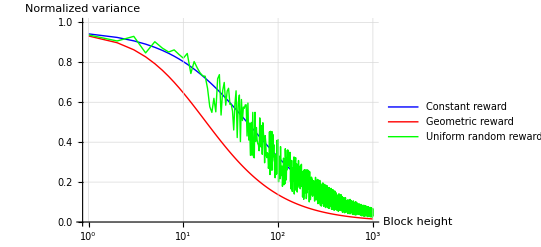

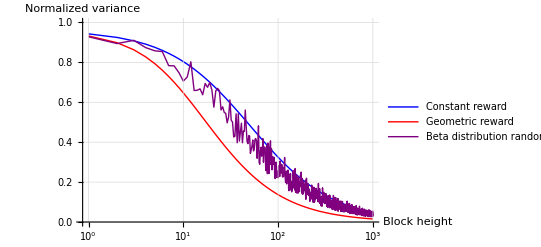

```mathematica
ListLinePlot[{datavarconst, datavargeo, datavaruni},PlotRange -> {0, 1.0}, DataRange->{0,time}, AxesLabel->{"Block height", "Normalized variance"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, PlotStyle-> {Blue, Red, Green}, PlotLegends->{"Constant reward", "Geometric reward", "Uniform random reward"}, ScalingFunctions-> {"Log10", None}]
ListLinePlot[{datavarconst, datavargeo, datavarbeta},PlotRange -> {0, 1.0}, DataRange->{0,time}, AxesLabel->{"Block height", "Normalized variance"}, PlotTheme->"Classic", GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}, PlotStyle-> {Blue, Red, Purple}, PlotLegends->{"Constant reward", "Geometric reward", "Beta distribution random reward"}, ScalingFunctions-> {"Log10", None}]
```

```mathematica
ListLinePlot[datavarbeta]
```